```mathematica
Quit[]
```

```mathematica
"Units:"
"Time: years"
"Length: pc"
"Mass: Solar mass"
a:=20000(*20 000 pc = 20kpc*)
M:=10^12(*Solar masses*)
m:=4*10^6(*Solar masses*)
G:=4.49*10^-15(*pc^3/(solar mass * yr^2)*)
c:=0.3064(*pc/yr*)
Subscript[m, p]:=10^-3(*Solar mass *)
Rs:=2(G m)/c^2
```

Units:

Time: years

Length: pc

Mass: Solar mass

```mathematica
Quit[]
```

```mathematica
"Potential and 4-velocity"
Φ[r_]:=-(G M)/(a+r)
fourVelocity[ΕN_,L_]:=√(2 ΕN/Subscript[m, p]-2Φ[r]-(L/(Subscript[m, p] r))^2)
"Which equals ( in dimensionless energy and angular mom. )"
√(2 ΕN/Subscript[m, p]-2Φ[r]-(L/(Subscript[m, p] r))^2)/.ΕN->-(G M)/a ϵ/.L->√(a G M)L/.Subscript[m, p]-> 1//FullSimplify
```

Potential and 4-velocity

Which equals ( in dimensionless energy and angular mom. )

√(G M (-(a L^2)/r^2+2/(a+r)-(2 ϵ)/a))

```mathematica
"Conversion between relativistic and newtonian energy"
RelativisticToNewtonian[Ε_]:=Subscript[m, p]/2(Ε^2/(c^2 Subscript[m, p]^2)-c^2)
```

Conversion between relativistic and newtonian energy

```mathematica
"Roots of the equation (limits of integration)"
R1[ΕN_,L_]:=Root[-a L^2-L^2 #1+2 ΕN #1^3 Subscript[m, p]+#1^2 (2 a ΕN Subscript[m, p]+2 G M Subscript[m, p]^2)&,1]
R2[ΕN_,L_]:=Root[-a L^2-L^2 #1+2 ΕN #1^3 Subscript[m, p]+#1^2 (2 a ΕN Subscript[m, p]+2 G M Subscript[m, p]^2)&,2]
R3[ΕN_,L_]:=Root[-a L^2-L^2 #1+2 ΕN #1^3 Subscript[m, p]+#1^2 (2 a ΕN Subscript[m, p]+2 G M Subscript[m, p]^2)&,3]
radialAction[ΕN_,L_]:=NIntegrate[fourVelocity[ΕN,L],{r,R2[ΕN,L],R3[ΕN,L]}]
```

Roots of the equation (limits of integration)

Plot values

Plot values:

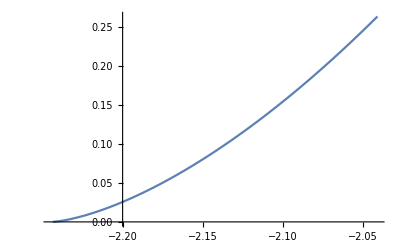

```mathematica
"Plot values"
"Plot values:"
Lmax:=1.5552632176183547*10^-7
Plot[radialAction[ΕN,Lmax*0.5],{ΕN,Φ[a]/500,Φ[a]/550}]
```

```mathematica
"Some test values:"
Lmax*0.5
radialAction[-2.1*10^-10,Lmax*0.5]
```

7.77632×10^-8

0.154553

```mathematica
"Derivation of the limits for L"
Reduce[G M (-(a L^2)/r^2+2/(a+r)-(2 ϵ)/a)>0&&G>0&&M>0&&a>0&&r>0&&ϵ>0,r,Reals]//FullSimplify
```

Derivation of the limits

a>0&&G>0&&M>0&&0<ϵ<1&&((L==0&&0<r<Root[(-a+a ϵ) #1^2+ϵ #1^3&,3])||(Root[a^3 L^2+a^2 L^2 #1+(-2 a+2 a ϵ) #1^2+2 ϵ #1^3&,2]<r<Root[a^3 L^2+a^2 L^2 #1+(-2 a+2 a ϵ) #1^2+2 ϵ #1^3&,3]&&((L>0&&√(-20+1/ϵ-8 ϵ+(1+8 ϵ)^(3/2)/ϵ)>2 L)||-1/2 √(-20+1/ϵ-8 ϵ+(1+8 ϵ)^(3/2)/ϵ)<L<0)))

```mathematica
"Derivation of the limits for eps"
Reduce[G M (-(a L^2)/r^2+2/(a+r)-(2 ϵ)/a)>0&&G>0&&M>0&&a>0&&r>0&&ϵ>0,ϵ,Reals]//FullSimplify
"Now we use the (one line above) result to derive:"
Limit[-(a^2 L^2)/r^2+(2 a)/(a+r),r->∞]
Limit[-(a^2 L^2)/r^2+(2 a)/(a+r),r->4G m]//FullSimplify
```

Derivation of the limits for eps

r>0&&a>0&&L+(√2 r)/(√(a (a+r)))>0&&(√2 r)/(√(a (a+r)))>L&&M>0&&G>0&&ϵ>0&&(a^2 L^2)/r^2+2 ϵ<(2 a)/(a+r)

Now we use the (one line above) result to derive:

0

-(a^2 L^2)/(16 G^2 m^2)+(2 a)/(a+4 G m)